## Solving the system of difference equations numerically

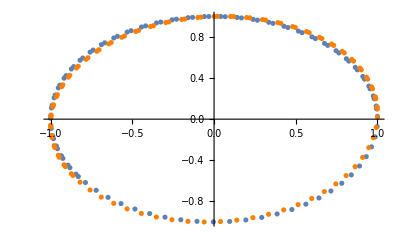

```mathematica
sys:={Subscript[x, 1][n + 1]- (0.995+a) Subscript[x, 1][n] + 0.1 Subscript[x, 2][n] == 0, Subscript[x, 2][n + 1]- 0.1 Subscript[x, 1][n] - (0.995+b) Subscript[x, 2][n] == 0,Subscript[x, 1][0]==Subscript[x, 10],Subscript[x, 2][0]==Subscript[x, 20]}

(*You can vary the initial conditions here*)
Subscript[x, 10]=1;
Subscript[x, 20]=0;

(*Solving the system for matrix A*)
a=0;
b=0;
sol=RSolveValue[sys, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}]; (*This gives us our vector as an ordered double solution*)
m1[n_]=sol[[1]]; 
m2[n_]=sol[[2]];
plot1=ListPlot[Table[{m1[i], m2[i]}, {i, 100}]];


(*Solving the system for matrix B*)
a=0.005;
b=-0.005;
sol2=RSolveValue[sys, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}];
m12[n_]=sol2[[1]];
m22[n_]=sol2[[2]];
plot2=ListPlot[Table[{m12[i], m22[i]}, {i, 100}],PlotStyle->Orange];
Show[plot1,plot2]
```

## Eigenstuffs and Diagonalization

The eigenvectors of A is: (0.707107+0. ⅈ
0.-0.707107 ⅈ) and (0.707107+0. ⅈ
0.+0.707107 ⅈ) and eigenvalues 0.995+0.1 ⅈ and 0.995-0.1 ⅈ. The first eigenvector
has real part (0.707107
0.) and imaginary part (0.
-0.707107) .

The eigenvectors of B is: (0.707107+0. ⅈ
0.0353553-0.706222 ⅈ) and (0.707107+0. ⅈ
0.0353553+0.706222 ⅈ) and eigenvalues 0.995+0.0998749 ⅈ and 0.995-0.0998749 ⅈ. The first eigenvector
has real part (0.707107
0.0353553) and imaginary part (0.
-0.706222) .

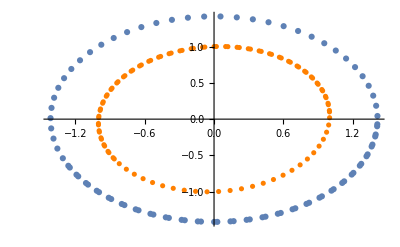

Diagonalized matrix A is: (0.995+0.1 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.995-0.1 ⅈ).

Diagonalized matrix B is: (0.995+0.0998749 ⅈ | 1.11022×10^-16-6.93889×10^-18 ⅈ
0.+1.04083×10^-17 ⅈ | 0.995-0.0998749 ⅈ).

Dot Product of real part and imaginary part of A is: 0.. They're orthogonal.

Dot Product of real part and imaginary part of A is: 1.93076×10^-32. They're orthogonal(?).

The norm of the eigenvector of diagonalized A are: 1. for Real 
and 0. for imaginary

The norm of the eigenvector of diagonalized B are: 1. for Real 
and 5.55807×10^-16 for imaginary

```mathematica
A={{0.995,-0.1},{0.1,0.995}};
B={{1,-0.1},{0.1, 0.99}};


eigA=Eigenvalues[A];
eigB=Eigenvalues[B];
eigvA=Eigenvectors[A];
eigvB=Eigenvectors[B];


StringForm["The eigenvectors of A is: `` and `` and eigenvalues `` and ``. The first eigenvector
has real part `` and imaginary part `` .",
eigvA[[1]]//MatrixForm, eigvA[[2]]//MatrixForm, eigA[[1]],eigA[[2]], 
Re[eigvA[[1]]]//MatrixForm, Im[eigvA[[1]]]//MatrixForm]

StringForm["The eigenvectors of B is: `` and `` and eigenvalues `` and ``. The first eigenvector
has real part `` and imaginary part `` .",
eigvB[[1]]//MatrixForm, eigvB[[2]]//MatrixForm, eigB[[1]],eigB[[2]], 
Re[eigvB[[1]]]//MatrixForm, Im[eigvB[[1]]]//MatrixForm]


Subscript[P, A]=Transpose[{Re[Eigenvectors[A][[1]]],Im[Eigenvectors[A][[1]]]}];
Subscript[P, B]=Transpose[{Re[Eigenvectors[B][[1]]],Im[Eigenvectors[B][[1]]]}];


(*Application of inverse of P increased the circle's radius by from 1 to 1.5*)
a=0.005;
b=-0.005;
sol=RSolveValue[sys, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}];
solp=Inverse[Subscript[P, B]].sol;
m1p[n_]=solp[[1]];
m2p[n_]=solp[[2]];
plotp=ListPlot[Table[{m1p[i], m2p[i]}, {i, 90}]];
Show[plot2,plotp,PlotRange->3]

(*Constructing the Transition Matrix*)
Subscript[T, A<-i]=Transpose[{Eigenvectors[A][[1]],Eigenvectors[A][[2]]}];
Subscript[T, B<-i]=Transpose[{Eigenvectors[B][[1]],Eigenvectors[B][[2]]}];

(*Diagonalizing: I can't see why the matrices aren't properly diagonalized.
The diagonal elements are correct so I think it is machine error.*)
DA=Inverse[Subscript[T, A<-i]].A.Subscript[T, A<-i];
DB=Inverse[Subscript[T, B<-i]].B.Subscript[T, B<-i];
StringForm["Diagonalized matrix A is: ``.",
DA//MatrixForm]
StringForm["Diagonalized matrix B is: ``.",
DB//MatrixForm]

(*Imaginary parts have smol dot product, so I guess "quite" orthogonal? Is this just machine error?*)
StringForm["Dot Product of real part and imaginary part of A is: ``. They're orthogonal.",
Re[Eigenvectors[DA][[1]]].Im[Eigenvectors[DA][[1]]]]

StringForm["Dot Product of real part and imaginary part of A is: ``. They're orthogonal(?).",
Re[Eigenvectors[DB][[1]]].Im[Eigenvectors[DB][[1]]]]


(*Real parts have unit norm while imaginary parts have ~0 norms*)
StringForm["The norm of the eigenvector of diagonalized A are: `` for Real 
and `` for imaginary", Norm[Re[Eigenvectors[DA][[1]]]], Norm[Im[Eigenvectors[DA][[1]]]]] 

StringForm["The norm of the eigenvector of diagonalized B are: `` for Real 
and `` for imaginary", Norm[Re[Eigenvectors[DB][[1]]]], Norm[Im[Eigenvectors[DB][[1]]]]]
```

## I tried scaling the system but it gives me precision error. Instead, I just plotted a semi-circle by limiting the number of data points

1.01

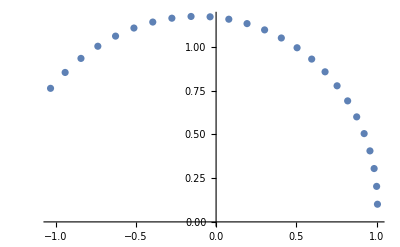

```mathematica
sysd:={Subscript[x, 1][n + 1]- d*(0.995+a) Subscript[x, 1][n] + d*0.1 Subscript[x, 2][n] == 0, Subscript[x, 2][n + 1]- d*0.1 Subscript[x, 1][n] - d*(0.995+b) Subscript[x, 2][n] == 0,Subscript[x, 1][0]==Subscript[x, 10],Subscript[x, 2][0]==Subscript[x, 20]}
(*Notice that I introduced a scaling factor d*)

(*You can vary the initial conditions here*)
Subscript[x, 10]=1;
Subscript[x, 20]=0;

d=1.01
(*Solving the system for matrix A*)
a=0;
b=0;
sol=RSolveValue[sysd, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}]; (*This gives us our vector as an ordered double solution*)
m1[n_]=sol[[1]]; 
m2[n_]=sol[[2]];
plot1=ListPlot[Table[{m1[i], m2[i]}, {i, 25}]]

(*Scaling A by 1.01 stretched the circle in both axes into an ellipse*)
```

0.99

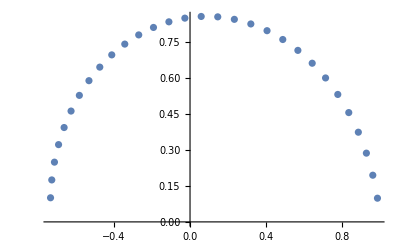

```mathematica
sysd:={Subscript[x, 1][n + 1]- d*(0.995+a) Subscript[x, 1][n] + d*0.1 Subscript[x, 2][n] == 0, Subscript[x, 2][n + 1]- d*0.1 Subscript[x, 1][n] - d*(0.995+b) Subscript[x, 2][n] == 0,Subscript[x, 1][0]==Subscript[x, 10],Subscript[x, 2][0]==Subscript[x, 20]}
(*Notice that I introduced a scaling factor d*)

(*You can vary the initial conditions here*)
Subscript[x, 10]=1;
Subscript[x, 20]=0;

d=0.99
(*Solving the system for matrix A*)
a=0;
b=0;
sol=RSolveValue[sysd, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}]; (*This gives us our vector as an ordered double solution*)
m1[n_]=sol[[1]]; 
m2[n_]=sol[[2]];
plot1=ListPlot[Table[{m1[i], m2[i]}, {i, 30}]]

(*Scaling A by 0.99 shrunk the circle in both axes into an ellipse*)
```

1.01

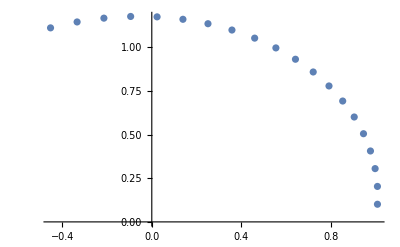

```mathematica
sysd:={Subscript[x, 1][n + 1]- d*(0.995+a) Subscript[x, 1][n] + d*0.1 Subscript[x, 2][n] == 0, Subscript[x, 2][n + 1]- d*0.1 Subscript[x, 1][n] - d*(0.995+b) Subscript[x, 2][n] == 0,Subscript[x, 1][0]==Subscript[x, 10],Subscript[x, 2][0]==Subscript[x, 20]}
(*Notice that I introduced a scaling factor d*)

(*You can vary the initial conditions here*)
Subscript[x, 10]=1;
Subscript[x, 20]=0;

d=1.01
(*Solving the system for matrix A*)
a=0.005;
b=-0.005;
sol=RSolveValue[sysd, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}]; (*This gives us our vector as an ordered double solution*)
m1[n_]=sol[[1]]; 
m2[n_]=sol[[2]];
plot1=ListPlot[Table[{m1[i], m2[i]}, {i, 20}]]

(*Scaling B by 1.01 stretched the circle in both axes into an ellipse*)
```

0.99

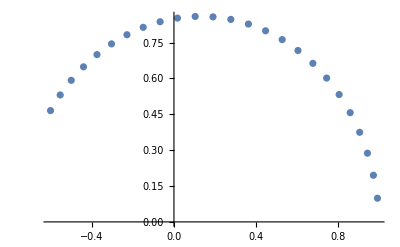

```mathematica
sysd:={Subscript[x, 1][n + 1]- d*(0.995+a) Subscript[x, 1][n] + d*0.1 Subscript[x, 2][n] == 0, Subscript[x, 2][n + 1]- d*0.1 Subscript[x, 1][n] - d*(0.995+b) Subscript[x, 2][n] == 0,Subscript[x, 1][0]==Subscript[x, 10],Subscript[x, 2][0]==Subscript[x, 20]}
(*Notice that I introduced a scaling factor d*)

(*You can vary the initial conditions here*)
Subscript[x, 10]=1;
Subscript[x, 20]=0;

d=0.99
(*Solving the system for matrix A*)
a=0.005;
b=-0.005;
sol=RSolveValue[sysd, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}]; (*This gives us our vector as an ordered double solution*)
m1[n_]=sol[[1]]; 
m2[n_]=sol[[2]];
plot1=ListPlot[Table[{m1[i], m2[i]}, {i, 25}]]

(*Scaling B by 0.99 shrunk the circle in both axes into an ellipse*)
```

## And like the rest of the tasks give me precision errors. I plan on plotting like the task said but it seems that my code can’t handle large values of iterations. Maybe my approach to the problem is wrong.

General::munfl: 1/2.^9441. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/5.^6294. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.^9441. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

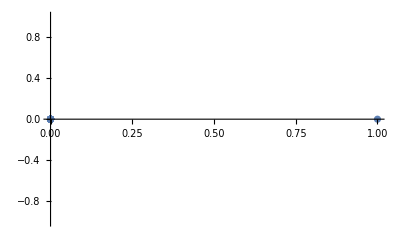

```mathematica
sys:={Subscript[x, 1][n + 1]- (0.995+a) Subscript[x, 1][n] + 0.1 Subscript[x, 2][n] == 0, Subscript[x, 2][n + 1]- 0.1 Subscript[x, 1][n] - (0.995+b) Subscript[x, 2][n] == 0,Subscript[x, 1][0]==Subscript[x, 10],Subscript[x, 2][0]==Subscript[x, 20]}

(*You can vary the initial conditions here*)
Subscript[x, 10]=1;
Subscript[x, 20]=0;

(*Solving the system for matrix A*)
a=0;
b=0;
sol=RSolveValue[sys, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}]; (*This gives us our vector as an ordered double solution*)
m1[n_]=sol[[1]]; 
m2[n_]=sol[[2]];
plot1=ListPlot[Table[{m1[i], m2[i]}, {i, 0, 100000, 3147}]]
```